## Prepare

```mathematica
imgsize=700;
imgpadding={{70, 20}, {50, 10}};
```

Always use the first element in the vector to be the component of small eigenvalue.

## Modules, Initial Condition and Parameters

### Modules

Rotation matrices

Rotation from vacuum to instantaneous matter basis

```mathematica
vac2instRotation[α0_,θv_]:=Module[{thetaxConst,alpha0=α0,thetav=θv},thetaxConst=ArcSin[Sin[2thetav]/(√(1+(alpha0)^2-2(alpha0)Cos[2thetav]))]/2;{{Cos[thetav-thetaxConst],Sin[thetav-thetaxConst]},{-Sin[thetav-thetaxConst],Cos[thetav-thetaxConst]}}]
```

Test Rotation

```mathematica
vac2instRotationTest=Module[{θv=ArcSin@√0.307},Grid[{{"Zero Matter Potential: "<>ToString@vac2instRotation[0,θv]},{"MSW Resonance: "<>ToString@vac2instRotation[Cos[2*θv],θv]}}]]
```

Zero Matter Potential: {{1., 0.}, {0., 1.}}
MSW Resonance: {{0.980433, -0.196852}, {0.196852, 0.980433}}

Conversion from length (km) to energy (eV): 197 MeV*fm=1 =>

```mathematica
km2eV[km_]:=Module[{length=km},km*10^(18)/(197*10^6)]
```

```mathematica
km2eVTest="1/1fm is "<>ToString[1/km2eV[10^(-18)]]<>"eV"
```

1/1fm is 197000000eV

#### Paramters

Paramters are grabbed from Kneller’s paper

#### Initial Condition

In (averaged) matter basis

```mathematica
θv=0.573;
energy=20*10^6; (* eV *)
deltam2=3*10^(-3); (* eV^2 *)
(* The following are calculated *)
omegav=deltam2/(2energy); (* 7.5*10^(-11) *) (*eV, delta^2m= 3*10^(-3)eV^2, E =20MeV*)
α0=Cos[2θv]/2;
α1=0.1α0;
β=(2Pi/km2eV[5.27])/omegav;
```

The initial condition in matter basis

```mathematica
initMatter={1,0}
```

{1,0}

Rotate to vacuum eigenbasis

```mathematica
initVac=vac2instRotation[α0,θv].initMatter
```

{0.994885,0.101012}

```mathematica
endpoint=800;
```

## Equation Solving

### Solving in Matter Basis

This problem can be solved in matter basis,hw

```mathematica
eqn1= I c1'[x]==Cos[2θv]/2(α0+α1 Cos[β x])c1[x]+Sin[2θv]/2(α0+α1 Cos[β x])c2[x]Exp[-I x]
eqn2=I c2'[x]==-Cos[2θv]/2(α0+α1 Cos[β x])c2[x]+ Sin[2θv]/2(α0+α1 Cos[β x])c1[x] Exp[I x]
```

ⅈ c1'[x]==0.206068 c1[x] (0.206068+0.0206068 Cos[3.13166 x])+0.455561 ⅇ^(-ⅈ x) c2[x] (0.206068+0.0206068 Cos[3.13166 x])

ⅈ c2'[x]==0.455561 ⅇ^(ⅈ x) c1[x] (0.206068+0.0206068 Cos[3.13166 x])-0.206068 c2[x] (0.206068+0.0206068 Cos[3.13166 x])

```mathematica
solVac=NDSolve[{eqn1,eqn2,c1[0]==initVac[[1]],c2[0]==initVac[[2]]},{c1,c2},{x,0,endpoint}]
```

{{c1→InterpolatingFunction[{{0., 800.}}, <>],c2→InterpolatingFunction[{{0., 800.}}, <>]}}

Check normalization

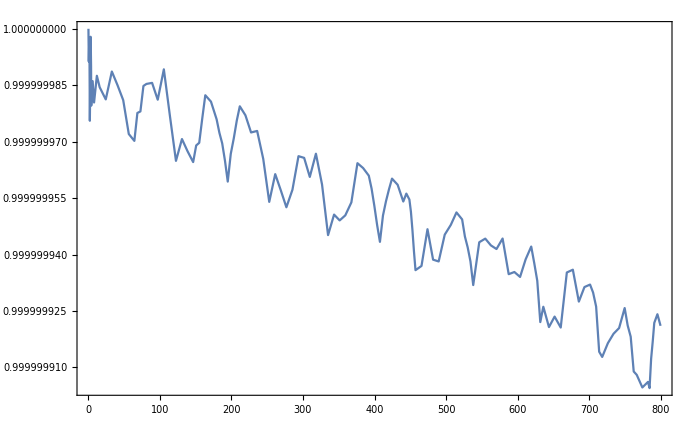

```mathematica
normVac=Plot[Evaluate[Abs[c1[x]]^2+Abs[c2[x]]^2/.solVac[[1]]],{x,0,endpoint},PlotRange->All,ImageSize->imgsize,Frame->True]
```

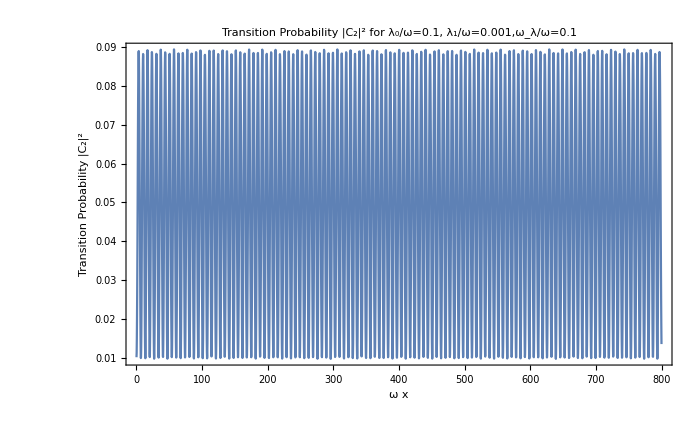

```mathematica
probVac=Plot[Evaluate[Abs[c2[x]]^2/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.solVac[[1]]],{x,0,endpoint},PlotRange->All,PlotLabel->"Transition Probability |C_2|^2 for λ_0/ω=0.1, λ_1/ω=0.001,ω_λ/ω=0.1",ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_2|^2"},ImagePadding->imgpadding]
```

Wavefunction in matter basis is

```mathematica
instWaveFunction[x_]=vac2instRotation[α0,θv].{c1[x],c2[x]}/.solVac[[1]]
```

{-0.101012 InterpolatingFunction[{{0., 800.}}, <>][x]+0.994885 InterpolatingFunction[{{0., 800.}}, <>][x],0.994885 InterpolatingFunction[{{0., 800.}}, <>][x]+0.101012 InterpolatingFunction[{{0., 800.}}, <>][x]}

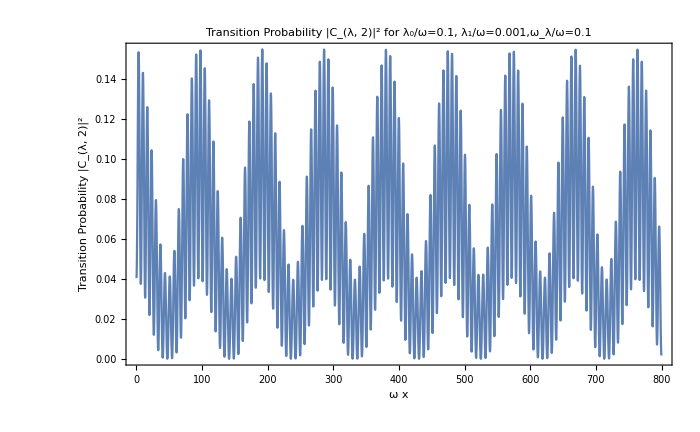

```mathematica
probInstHeavy=Plot[Evaluate[Abs[instWaveFunction[x][[2]]]^2/.solVac[[1]]],{x,0,endpoint},PlotRange->All,PlotLabel->"Transition Probability |C_(λ, 2)|^2 for λ_0/ω=0.1, λ_1/ω=0.001,ω_λ/ω=0.1",ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_(λ, 2)|^2"},ImagePadding->imgpadding]
```